### Illustration/Example of Spivak Chapter 3, Problem 6(b)

```mathematica
x1=2;
x2=5;
x3=7;
x4=10;
```

```mathematica
f4[x_]:=((x-x1)(x-x2)(x-x3))/((x4-x1)(x4-x2)(x4-x3))
```

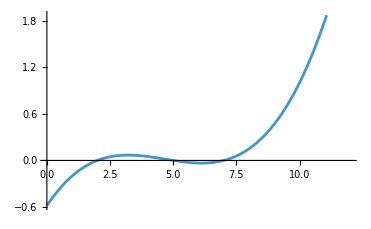

```mathematica
Plot[f4[x],{x, 0,12}]
```

```mathematica
f3[x_]:=((x-x1)(x-x2)(x-x4))/((x3-x1)(x3-x2)(x3-x4))
```

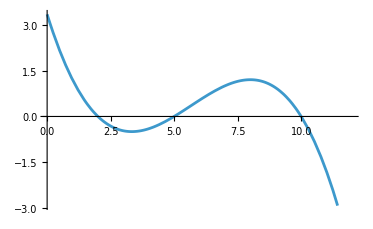

```mathematica
Plot[f3[x],{x, 0,12}]
```

```mathematica
f2[x_]:=((x-x1)(x-x3)(x-x4))/((x2-x1)(x2-x3)(x2-x4))
```

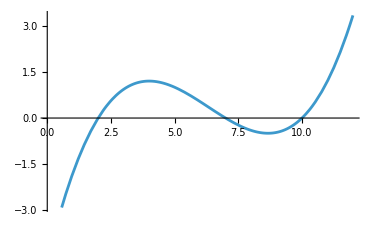

```mathematica
Plot[f2[x],{x, 0,12}]
```

```mathematica
f1[x_]:=((x-x2)(x-x3)(x-x4))/((x1-x2)(x1-x3)(x1-x4))
```

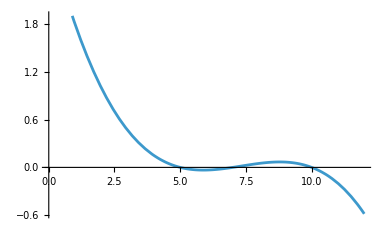

```mathematica
Plot[f1[x],{x, 0,12}]
```

```mathematica
g[x_]:=8f1[x]+6f2[x]+4f3[x]+2f4[x]
```

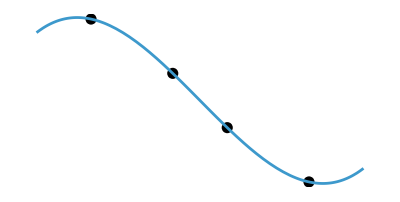

```mathematica
Show[Graphics[Style[Point[{{2,8},{5,6},{7,4},{10,2}}],PointSize[0.02]]],Plot[g[x],{x, 0,12}]]
```